# Quantum Benchmarks

## HHL Matrix Creation

## Preliminaries

## Gates

```mathematica
Clear[Ctrl,Phase]
Ctrl[gate_]:=Ctrl[gate]=ArrayFlatten[{{Id,0},{0,gate}}]
Phase[ϕ_,pauli_]:=Phase[ϕ,pauli]=MatrixExp[-ⅈ ϕ pauli]

{Id,X,Y,Z}=PauliMatrix/@{0,1,2,3};
H={{1,1},{1,-1}}/√2;
CNOT=Ctrl[X];
CZ=Ctrl[Z];
SWAP=ArrayFlatten[{{1,0,0},{0,X,0},{0,0,1}}];
SQSWAP=MatrixPower[SWAP,1/2];
NOTC=SWAP.CNOT.SWAP;
MyEcho[x_]:=Module[{},Print[x//MatrixForm];x]
```

```mathematica
MatrixForm/@{Id,X,Y,Z,H,CNOT,CZ,SWAP,SQSWAP,NOTC,Phase[Z,π/2],Phase[Y,π/16]}
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0),(-ⅈ | 0
0 | ⅈ),(Cos[π/16] | -Sin[π/16]
Sin[π/16] | Cos[π/16])}

## Matrix Circuits

## VQE Ansatz for U

We seek an ansatz which is interleaved single-qubit and entangling layers; much like a VQE circuit. This is an arbitrary choice of course.

```mathematica
Clear[VQEAnsatz]
VQEAnsatz[width_Integer/;width≥2,blockSize_Integer/;blockSize≥2,depth_Integer/;depth≥1,singleQubitGateCount_Integer/;singleQubitGateCount≥1]:=Flatten@Join[Table[{
SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width],
EntanglingLayer@@If[EvenQ@width,
If[EvenQ@i,
{{1}}~Join~Partition[Range[2,width-1],2]~Join~{{width}},
Reverse/@Reverse@Partition[Reverse@Range[width],2]
],
If[EvenQ@i,
Partition[Range[width],UpTo[2]],
Reverse/@Reverse@Partition[Reverse@Range[width],UpTo[2]]
]
]
},
{i,1,depth}
],{SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width]}
]

Clear[UnitaryMatrixListQ,GateSetQ,RandomVQESample]
UnitaryMatrixListQ[list_]:=ListQ[list]∧(Length@list>0)∧And@@(UnitaryMatrixQ/@list)∧Equal@@(Dimensions/@list)∧(Dimensions@First@list=={2,2})
GateSetQ[assoc_]:=AssociationQ[assoc]∧UnitaryMatrixListQ@Values[assoc]
Clear[kron]
kron[mat_?MatrixQ]:=mat
kron[other__]:=KroneckerProduct[other]
RandomVQESample[width_Integer/;width≥2,blockSize_Integer/;blockSize≥2,depth_Integer/;depth≥1,entanglingGate_?UnitaryMatrixQ,entanglingGateName_String,singleQubitGates_?GateSetQ,numeric_:True]:=
Module[{
singleQubitGatesN=Values@singleQubitGates//If[numeric,N,Identity],
entanglingGateN=entanglingGate//If[numeric,N,Identity],
ansatz,U,textual
},
ansatz=VQEAnsatz[width,blockSize,depth,Length@singleQubitGates];
U=Dot@@(ansatz//.{
SingleQubitLayer[l___,gateIdx_Integer,r___]:>SingleQubitLayer[l,singleQubitGatesN⟦gateIdx⟧,r],
EntanglingLayer[l___,gateIdcs_?VectorQ,r___]:>EntanglingLayer[l,If[Length@gateIdcs==1,Id,entanglingGateN],r]
}/.{
SingleQubitLayer->kron,
EntanglingLayer->kron
}
);
textual=ansatz//.{
SingleQubitLayer[gateIdcs__]:>MapIndexed[Function[{idx,lane},Keys[singleQubitGates]⟦idx⟧<>" "<>ToString[lane⟦1⟧]],{gateIdcs}],
EntanglingLayer[gateIdcs__]:>(If[Length@#==1,Nothing,entanglingGateName<>" "<>StringRiffle[ToString/@#, " "]]&/@{gateIdcs})
}//Flatten;

<|
"ansatz"->ansatz,
"textual"->(textual//Reverse),
"U"->U//Chop,
"B"->U[[-blockSize;;,-blockSize;;]]//Chop,
(*"Histogram"->(Table[(Abs[#^2]&)/@((U[[1;;blockSize,1;;blockSize]]//Inverse).IdentityMatrix[blockSize][[k]]),{k,1,blockSize}]//Transpose),*)
"Histogram"->(Table[(Abs[#^2]&)/@((U[[-blockSize;;,-blockSize;;]]//PseudoInverse).IdentityMatrix[blockSize][[k]]),{k,1,blockSize}]//Transpose),
"qubits"->Log[2,Length[U]]
|>
]
```

```mathematica
VQEAnsatz[4,2,2,5]
```

{SingleQubitLayer[4,1,3,1],EntanglingLayer[{1,2},{3,4}],SingleQubitLayer[4,5,4,4],EntanglingLayer[{1},{2,3},{4}],SingleQubitLayer[2,2,5,4]}

The RandomVQESample function expects a circuit width (i.e. how many qubits U should act on), an ansatz depth, an entangling gate plus name, and a single qubit gate list defined in the following. This can of course be changed to include other rotations.

```mathematica
gateset=<|
"I"->IdentityMatrix[2],
"X"->X,
"Y"->Y,
"Z"->Z,
"R"->Phase[Z,π/3],
"S"->Phase[Z,π/4],
"T"->Phase[Z,π/8],
"RX"->Phase[X,π/3],
"SX"->Phase[X,π/4],
"TX"->Phase[X,π/8],
"RY"->Phase[Y,π/3],
"SY"->Phase[Y,π/4],
"TY"->Phase[Y,π/8]
|>;
MatrixForm/@%
```

<|I→(1 | 0
0 | 1),X→(0 | 1
1 | 0),Y→(0 | -ⅈ
ⅈ | 0),Z→(1 | 0
0 | -1),R→(ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)),S→(ⅇ^(-(ⅈ π)/4) | 0
0 | ⅇ^((ⅈ π)/4)),T→(ⅇ^(-(ⅈ π)/8) | 0
0 | ⅇ^((ⅈ π)/8)),RX→(1/2 (-1)^(1/3)-1/2 (-1)^(2/3) | -1/2 (-1)^(1/3)-1/2 (-1)^(2/3)
-1/2 (-1)^(1/3)-1/2 (-1)^(2/3) | 1/2 (-1)^(1/3)-1/2 (-1)^(2/3)),SX→(1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2)),TX→(1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | -1/2 (-1)^(1/8)-1/2 (-1)^(7/8)
-1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)-1/2 (-1)^(7/8)),RY→(1/2 | -(√3)/2
(√3)/2 | 1/2),SY→(1/(√2) | -1/(√2)
1/(√2) | 1/(√2)),TY→(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])|>

```mathematica
RandomVQESample[2,2,3,CZ,"CZ",gateset]
```

<|ansatz→{SingleQubitLayer[9,2],EntanglingLayer[{1,2}],SingleQubitLayer[6,10],EntanglingLayer[{1},{2}],SingleQubitLayer[1,12],EntanglingLayer[{1,2}],SingleQubitLayer[11,7]},textual→{T 2,RY 1,CZ 1 2,SY 2,I 1,TX 2,S 1,CZ 1 2,X 2,SX 1},U→{{0.+0.183013 ⅈ,0.683013,0.+0.683013 ⅈ,-0.183013},{0.-0.683013 ⅈ,0.183013,0.+0.183013 ⅈ,0.683013},{-0.683013,0.+0.183013 ⅈ,0.183013,0.+0.683013 ⅈ},{0.183013,0.+0.683013 ⅈ,0.683013,0.-0.183013 ⅈ}},B→{{0.183013,0.+0.683013 ⅈ},{0.683013,0.-0.183013 ⅈ}},Histogram→{{0.133975,1.86603},{1.86603,0.133975}},qubits→2|>

## Find Good Circuit Candidates

```mathematica
(* checks that the top bs x bs block has bs^2-minOffset many unique absolute value squared entries *)
Clear[CircuitCriterion]
CircuitCriterion[bs_Integer,threshold_:.01,minOffset_:1,distinctSVs_:2,conditonNum_:2,minProb_:0.2]:=Function[U,
(
Length@Union@Rationalize[#,threshold]&@Abs@N@Flatten@U⟦-bs;;,-bs;;⟧≥bs^2-minOffset
)∧(
(* condition number criterion *)
Max[SingularValueList[U⟦-bs;;,-bs;;⟧]]/ Min[SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteCases[#==0&]]<=conditonNum
)∧(
(* distinct singular values criterion *)
(SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteDuplicatesBy[#,Round[500*#]&]&//Length)≥distinctSVs
)∧(
(* enforce large probability entries in every column *)
(Apply[Max,Transpose[Abs[#]^2&/@PseudoInverse[U⟦-bs;;,-bs;;⟧]]*(Min[SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteCases[#==0&]])^2,1]//Min)>minProb
)
]
```

```mathematica
CircuitCriterion[5][RandomReal[{1,5},{10,10}]]&/@Range[10]
CircuitCriterion[5][IdentityMatrix[10]]
```

{True,True,True,True,True,True,True,False,True,True}

False

```mathematica
Clear[MatPlot]
MatPlot[U_?UnitaryMatrixQ,bs_Integer]:=BarChart3D[MyEcho[Abs[#]^2&/@U⟦-bs;;,-bs;;⟧],ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

Re-run the following or increase trials if it doesn’t print out a final matrix.

143+Match found after + trials

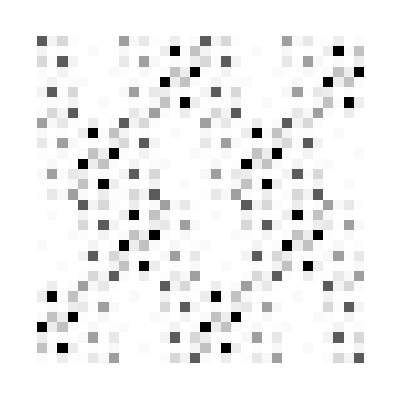

32

{0.965926,0.866025}

{SY 6,T 5,SX 4,T 3,S 2,S 1,CX 5 6,CX 3 4,CX 1 2,RY 6,TY 5,RY 4,T 3,T 2,RY 1,CX 4 5,CX 2 3,SY 6,I 5,X 4,S 3,R 2,TY 1,CX 5 6,CX 3 4,CX 1 2,X 6,X 5,Y 4,RY 3,I 2,S 1,CX 4 5,CX 2 3,TX 6,R 5,S 4,Z 3,SY 2,TX 1,CX 5 6,CX 3 4,CX 1 2,RY 6,SX 5,SY 4,TY 3,SX 2,X 1}

```mathematica
theVQE=Module[{
theVQE,
lowerRightBlockSize=32(* dimension *)
},

Module[{
width=6,  (* number of overall qubits *)
depth=4,  (* ansatz depth *)
entanglingGate=CNOT,
entanglingGateName="CX",
singleQubitGates=gateset,
i,maxTrials=10000,
criterionF=CircuitCriterion[lowerRightBlockSize,.007,2^20-100,2,2,0.2] (* play with the two threshold parameters in case you don't get a hit *)
},
For[i=1,i≤maxTrials,i++;
With[{
vqe=RandomVQESample[width,lowerRightBlockSize,depth,entanglingGate,entanglingGateName,singleQubitGates,True]
},
If[criterionF@vqe["U"],
theVQE=vqe;
Print["Match found after "+i+" trials"];
Break[];
]
]
]
];


(*MatPlot[theVQE["U"],lowerRightBlockSize]//Print;*)
theVQE
];

(Abs[#]^2&/@PseudoInverse[theVQE["B"]])//ArrayPlot
(*theVQE["B"]//MatrixForm*)
theVQE["B"]//SingularValueList;
%//Length
DeleteDuplicatesBy[%%,Round[500*#]&]
theVQE["textual"]
```

## Polynomial Coefficients

```mathematica
(*Finds the largest absolute value on the interval[-1,1]*)
findPolyMaxAbs[poly_]:=Module[{deriv=D[poly,x],roots,optimaCandidates},roots=If[TrueQ@Element[deriv,Complexes],{},x/.NSolve[deriv==0,x]];
optimaCandidates=Join[{-1},roots,{1}];
(poly/.x->optimaCandidates)//Abs//Max];
(*Lowest degree problem specific polynomial*)
fitOddPoly[singularValues_]:=fitOptimizedPoly[singularValues,0,1];
(*Optimise the magnitude of the polynomial on[-1,1]*)
fitOptimizedPoly[singularValues_,numExtraPoints_,numRandomTrials_]:=Module[{distinctSVs=DeleteDuplicates[singularValues],fitPoints,tmpPoly,currentMinMax=Infinity,currentBestPoly},
For[j=0,j<numRandomTrials,j++,fitPoints=Join[distinctSVs,Table[RandomReal[{0,2}],{k,1,numExtraPoints}]];
fitPoints=DeleteCases[Join[fitPoints,-fitPoints]//N,0.0];
tmpPoly=InterpolatingPolynomial[{#,1/#}&/@fitPoints,x];
tmpPoly=((tmpPoly-(tmpPoly/.x->-x))/2)//Simplify;
currentBestPoly=If[findPolyMaxAbs[tmpPoly]<currentMinMax,tmpPoly,currentBestPoly];
currentMinMax=If[findPolyMaxAbs[tmpPoly]<currentMinMax,findPolyMaxAbs[tmpPoly],currentMinMax];];
currentBestPoly];
```

8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9

{0.995078,0.936608,0.35037810813806799,0.0990974}

0.+112.125 x-1067.05 x^3+1909.86 x^5-954.93 x^7

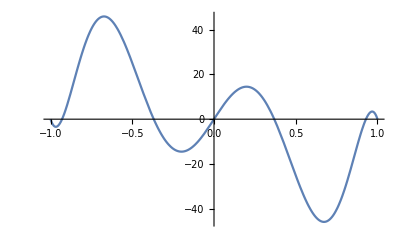

45.835

0.+114.27 x-1307.51 x^3+4198.18 x^5-5050.67 x^7+2047.87 x^9

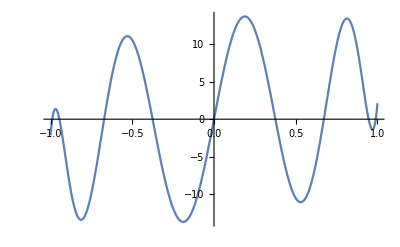

13.7394

```mathematica
(*Some tests and demos for the above*)
poly=8.1634015068251439828372895135544240474700927734375`30. x-93.53523368853274178036372177302837371826171875`30. x^3+301.21804475280686119731399230659008026123046875`30. x^5-363.1742884165829536868841387331485748291015625`30. x^7+147.482519204062327844440005719661712646484375`30. x^9
singularValues={0.99507773624,0.936608339348,0.350378108138067994,0.09909742093286229}
%//fitOddPoly
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
optPoly1=fitOptimizedPoly[%%%%,1,100]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
(*fitOptimizedPoly[%%%%%%%,2,10000]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs*)
```

```mathematica
(*Computes the pair of polynomials that correspond to the given real part, see more in https://arxiv.org/abs/1806.01838 *)
getPolyPairs[poly_,precision_]:=Module[{polyTry,K,roots,Qp,Zp,SRp,LRp,Ip,Wp,genRoots,zeroRoots,smallRealRoots,largeRealRoots,imgRoots,parityTrick,Bp,Cp},
polyTry=SetPrecision[poly,precision];
degree = (CoefficientList[polyTry,x]//Length)-1;
(K=Sqrt[-Coefficient[(1-polyTry^2//Expand),x^(2 degree)]])//Precision;
roots=x/.NSolve[(1-polyTry^2//Expand)==0,x,WorkingPrecision->precision];
(*p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]*)
(genRoots=Select[roots,(Re[#]>0&& Im[#]>0)&]);
zeroRoots=(Select[roots,(#==0)&]);
smallRealRoots=(Select[roots,(#!=0&&Re[#]>-1&&Re[#]<1&& Im[#]==0)&]);
(smallRealRoots=Table[smallRealRoots[[4i-3]],{i,1,(smallRealRoots//Length)/4}]);
(largeRealRoots=Select[roots,(Re[#]≥1&& Im[#]==0)&]);
(imgRoots=Select[roots,(Re[#]==0&& Im[#]>0)&]);
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@genRoots) ;
Zp=x^((zeroRoots//Length)/2);
SRp=(x^2-#^2)&/@smallRealRoots;
LRp=(Sqrt[#^2-1]x+I # Sqrt[1-x^2])&/@largeRealRoots;
Ip=(Sqrt[Abs[#]^2+1]x-I Abs[#]Sqrt[1-x^2])&/@imgRoots;
Wp=K*(Times@@Qp)*Zp*(Times@@SRp)*(Times@@LRp)*(Times@@Ip)//Expand//Simplify;
parityTrick=SetPrecision[Wp/.{Sqrt[1-x^2]->-I},precision];
Bp=SetPrecision[(parityTrick+(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
Cp=SetPrecision[(parityTrick-(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
{Bp,Cp}
]
```

True

8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

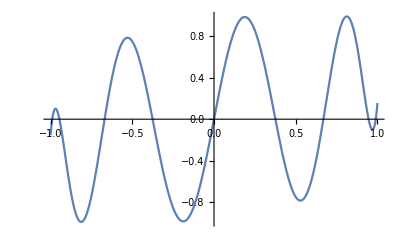

True

```mathematica
(*Some tests and demos for the above*)
{Bp,Cp}=getPolyPairs[ChebyshevT[5,x] ,110];
Bp^2+(1-x^2)Cp^2+ChebyshevT[5,x]^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
poly=8.163401506825144 x-93.53523368853274 x^3+301.21804475280686 x^5-363.17428841658295 x^7+147.48251920406233 x^9
Plot[%,{x,-1,1}]
{Bp,Cp}=getPolyPairs[poly,30];
poly=SetPrecision[poly,30];
Bp^2+(1-x^2)Cp^2+poly^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
```

```mathematica
(*Computes the sequence of angles for a given polynomial, see more in https://arxiv.org/abs/1806.01838 *)
getAngles[poly_,precision_Integer:10]:=Module[{tmpPoly,agreement,tmpprecision,Bp,Cp,Mat,carved,phs,phaseGates,W,NewMat},
agreement=1;
tmpprecision=MachinePrecision;
phs={};
While[ ((agreement//Accuracy) <precision) ||(agreement>10^-precision),
tmpPoly=SetPrecision[poly,tmpprecision];
{Bp,Cp}=getPolyPairs[tmpPoly,tmpprecision];
(Mat={{tmpPoly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,tmpPoly-I Bp}})//MatrixForm;
carved=NestList[carveLastAngle[#[[1]]]&,{Mat,{}},(tmpPoly//CoefficientList[#,x]&//Length)-1];
phs=Join[{(carved//Last)[[1]][[1]][[1]]},(#[[2]]&/@ carved)//Reverse//Most];
NewMat=getWMatrix[phs];
agreement=(NewMat[[1,1]]-tmpPoly-I Bp)//Expand//CoefficientList[#,x]&//Abs//Total;
Print[tmpprecision];
tmpprecision=2tmpprecision];
phs//Arg
];
carveLastAngle[Mat_]:=Module[{phase,outMat},
phase=(Coefficient[Mat[[1,1]],x,Exponent[Mat[[1,1]],x]]/(Coefficient[Mat[[1,2]]/.{Sqrt[1-x^2]->-I},x,(Exponent[Mat[[1,1]],x]-1)]))//Sqrt;
outMat=Mat.{{Conjugate[phase],0},{0,phase}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand;
outMat=outMat/.x^b_/;b≥Exponent[Mat[[1,1]],x]+1->0;
outMat=outMat/.Sqrt[1-x^2]x^b_/;b≥Exponent[Mat[[1,1]],x]->0;
{outMat, phase}
];
getWMatrix[phs_]:=Module[{phaseGates,W},
phaseGates=Table[{{phs[[i]],0},{0,Conjugate[phs[[i]]]}},{i,1,Length[phs]}];
(W={{x,I Sqrt[1-x^2]},{I Sqrt[1-x^2],x}})//MatrixForm;
(Dot@@((phaseGates//Most).W)).(phaseGates//Last)//Expand
];
WAnglesToRAngles[angles_]:=Module[{tmpAngles=angles},
tmpAngles[[1]]+=Last[angles]+((Mod[(Length[angles]),4])-1)Pi/2;
Mod[#,2 Pi]&/@Drop[tmpAngles,-1]-Pi/2];
getRMatrix[angles_]:=Module[{phaseGates,R},
phaseGates=Table[{{Exp[I angles[[i]]],0},{0,Exp[-I angles[[i]]]}},{i,1,Length[angles]}];
(R={{x, Sqrt[1-x^2]},{ Sqrt[1-x^2],-x}})//MatrixForm;
(Dot@@(phaseGates.R))//Expand
];
```

```mathematica
(*Some tests and demos for the above*)
angles=getAngles[ChebyshevT[10,x],20]//Chop
(getWMatrix[Exp[I%]])[[1,1]]-ChebyshevT[10,x]//Chop
(getRMatrix[%%//WAnglesToRAngles])[[1,1]]-ChebyshevT[10,x]//Expand//Chop
tmpPoly=poly/findPolyMaxAbs[poly]//Expand
angles=getAngles[%,20]
((getWMatrix[Exp[I%]//Reverse])[[1,1]]-%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
((getRMatrix[%%//WAnglesToRAngles])[[1,1]]-%%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
(*This is what we need to feed to the QSVT circuit*)
%%%//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.785398163397448309615660845819875721049292349843776,0,0,0,0,0,0,0,0,0,0.785398163397448309615660845819875721049292349843776455243736148}

0

0

8.27720505405564551123137 x-94.8391805023565269774823 x^3+305.417235733924878686473 x^5-368.237192923995131082338 x^7+149.538529045778466957024 x^9

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.408901635471894571772110507561051468532631544752781,0.3584552943894671048461378497305384989146988780925645,0.13603714837731554333554206592563397208622491414361709,0.0886809496145304613134064710023385996384743201663036807,-0.2528935548135681432431437582642864394177341833368914951,-0.252893554813568143243143758264286439417734183336891495115,0.08868094961453046131340647100233859963847432016630368068608,0.13603714837731554333554206592563397208622491414361708991167,0.358455294389467104846137849730538498914698878092564541323801,1.16189469132300204745921118407869997356595315493477190490618146}

0

0

{-1.21234,-1.43476,-1.48212,4.4595,4.4595,-1.48212,-1.43476,-1.21234,0.752993}

```mathematica
Clear[anglesForCircuit];
anglesForCircuit[vqe_Association,verbose_Symbol:False]:=Module[{
U=vqe["U"],
blockEncoding,
SVs,
interPolys, interPolysMaxAbs,
objectiveFunction, optimumDeg,
interPoly,
subnormalisation,
print=If[verbose,Print,Identity]
},
blockEncoding=U[[-Length[U]/2;;,-Length[U]/2;;]];
blockEncoding//MatrixForm//print;
If[verbose&&False,MatPlot[U,Length[blockEncoding]]//print,False];
blockEncoding//Inverse//MatrixForm//print;
If[verbose&&False,MatInvPlot[blockEncoding]//print,False];
blockEncoding.Inverse[blockEncoding]//MatrixForm//Chop//print;
SVs=SingularValueList[blockEncoding];
SVs=DeleteDuplicatesBy[SVs,Round[500*#]&];
print[SVs];
print[DeleteDuplicates[SVs]];
interPolys=Table[fitOptimizedPoly[SVs,i,100^i],{i,0,1}];
interPolysMaxAbs=findPolyMaxAbs/@interPolys;
For[i=1,i≤Length[interPolys],i++,Plot[interPolys[[i]],{ x,-1,1}]//print];
objectiveFunction=1/interPolysMaxAbs/(Length[CoefficientList[#,x]]&/@interPolys);
optimumDeg=(Position[objectiveFunction,Max[objectiveFunction]]//Flatten)[[1]];
print[optimumDeg];
interPoly=interPolys[[optimumDeg]];
subnormalisation=0.9999/findPolyMaxAbs[interPoly];
interPoly=subnormalisation*interPoly//Expand;
print[interPoly];
{subnormalisation,getAngles[interPoly,8]//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&}
];
Clear[MatInvPlot];
MatInvPlot[mat_]:=
BarChart3D[MyEcho[(Abs[#])^2&/@Inverse[mat]]//Transpose,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&;
```

```mathematica
anglesForCircuit[theVQE,True]
```

anglesForCircuit[theVQE$2500,True]

## Export Candidates to Python

```mathematica
exportCandidate[vqe_Association]:=Module[{str="",idleRemoved=vqe["textual"]//DeleteCases[#,x_/;StringTake[x,2]=="I "]&,angles,subnorm},
{subnorm,angles}=anglesForCircuit[vqe];
Print[subnorm];
str=str<>"{\n    \"qubits\": ";
str=str<>(vqe["qubits"]//ToString)<>",";
str=str<>"\n    \"ancillas\": 1,";
str=str<>"\n    \"circuit\": [";
str=str<>StringRiffle["("<>StringReplace["\""<>StringReplace[#," "->"\" ",1]," "->", "]<>")"&/@(idleRemoved),", "]<>"],\n";
str=str<>"    \"angles\": [";
str=str<>StringRiffle[ToString/@angles,", "]<>"],\n";
str=str<>"    \"histogram\": [\t";
str=str<>StringRiffle[("["<>StringRiffle[(ToString[#,CForm])&/@#,", "]<>"]")&/@(subnorm^2*vqe["Histogram"]),",\n\t\t\t\t\t"]<>"],\n";
str=str<>"}";
str
]
```

```mathematica
exportCandidate[theVQE]
```

MachinePrecision

0.83258

{
    "qubits": 6,
    "ancillas": 1,
    "circuit": [("SY", 6), ("T", 5), ("SX", 4), ("T", 3), ("S", 2), ("S", 1), ("CX", 5, 6), ("CX", 3, 4), ("CX", 1, 2), ("RY", 6), ("TY", 5), ("RY", 4), ("T", 3), ("T", 2), ("RY", 1), ("CX", 4, 5), ("CX", 2, 3), ("SY", 6), ("X", 4), ("S", 3), ("R", 2), ("TY", 1), ("CX", 5, 6), ("CX", 3, 4), ("CX", 1, 2), ("X", 6), ("X", 5), ("Y", 4), ("RY", 3), ("S", 1), ("CX", 4, 5), ("CX", 2, 3), ("TX", 6), ("R", 5), ("S", 4), ("Z", 3), ("SY", 2), ("TX", 1), ("CX", 5, 6), ("CX", 3, 4), ("CX", 1, 2), ("RY", 6), ("SX", 5), ("SY", 4), ("TY", 3), ("SX", 2), ("X", 1)],
    "angles": [3.87871, 3.87871, -0.852125],
    "histogram": [	[0.1844155116771273, 0.013240438025506871, 0.044335002279092255, 0.0031831099493667726, 0.000027269568956214084, 0.00037981609842417836, 6.555828144979084e-6, 0.0000913109067460317, 0.10809496957047784, 0.00776086963862746, 0.025986917687575096, 0.0018657767450641393, 0.0014805564813188251, 0.02062149156571014, 0.00035593792722012486, 0.004957575787684863, 0.18441551167712691, 0.013240438025506871, 0.04433500227909226, 0.0031831099493667366, 0.000027269568956214796, 0.0003798160984241723, 6.555828144980154e-6, 0.00009131090674602689, 0.10809496957047796, 0.007760869638627473, 0.025986917687575068, 0.0018657767450641163, 0.0014805564813188282, 0.02062149156571012, 0.0003559379272201219, 0.004957575787684857],
					[0.013240438025506857, 0.0009506206799687005, 0.0031831099493667575, 0.00022853701204241387, 0.00037981609842416785, 0.005290155808982242, 0.00009131090674603605, 0.00127179686629946, 0.007760869638627415, 0.0005572053703063287, 0.001865776745064123, 0.000133956743322678, 0.020621491565710106, 0.28722032543862325, 0.004957575787684873, 0.06905012310036793, 0.013240438025506845, 0.0009506206799686939, 0.0031831099493667588, 0.0002285370120424175, 0.0003798160984241861, 0.005290155808982205, 0.00009131090674603006, 0.0012717968662994275, 0.007760869638627438, 0.0005572053703063251, 0.0018657767450641106, 0.00013395674332268462, 0.020621491565710123, 0.287220325438623, 0.004957575787684871, 0.06905012310036793],
					[0.044335002279092255, 0.003183109949366781, 0.18441551167712733, 0.013240438025506888, 6.555828144979354e-6, 0.00009131090674603118, 0.000027269568956213786, 0.0003798160984241759, 0.025986917687575085, 0.0018657767450641159, 0.10809496957047804, 0.007760869638627479, 0.00035593792722011147, 0.004957575787684871, 0.001480556481318839, 0.020621491565710068, 0.044335002279092234, 0.003183109949366768, 0.18441551167712722, 0.013240438025506842, 6.555828144978667e-6, 0.00009131090674603284, 0.000027269568956219394, 0.00037981609842416855, 0.025986917687575033, 0.0018657767450641124, 0.10809496957047803, 0.007760869638627441, 0.0003559379272201221, 0.004957575787684843, 0.0014805564813188195, 0.0206214915657101],
					[0.0031831099493667583, 0.00022853701204242314, 0.013240438025506902, 0.0009506206799687112, 0.00009131090674602771, 0.001271796866299434, 0.00037981609842417576, 0.005290155808982207, 0.0018657767450641263, 0.0001339567433226794, 0.007760869638627432, 0.0005572053703063231, 0.004957575787684924, 0.06905012310036784, 0.02062149156571006, 0.2872203254386231, 0.003183109949366769, 0.00022853701204242507, 0.01324043802550686, 0.0009506206799687082, 0.00009131090674603107, 0.0012717968662994484, 0.0003798160984241612, 0.005290155808982224, 0.0018657767450641148, 0.00013395674332268364, 0.007760869638627418, 0.0005572053703063232, 0.004957575787684874, 0.06905012310036795, 0.020621491565710123, 0.28722032543862297],
					[0.0009506206799687059, 0.013240438025506897, 0.00022853701204241954, 0.003183109949366765, 0.0052901558089822245, 0.00037981609842416855, 0.0012717968662994557, 0.00009131090674603136, 0.0005572053703063408, 0.007760869638627465, 0.00013395674332267567, 0.0018657767450641178, 0.28722032543862264, 0.02062149156571007, 0.06905012310036783, 0.004957575787684832, 0.0009506206799687288, 0.013240438025506845, 0.00022853701204241758, 0.003183109949366721, 0.005290155808982196, 0.00037981609842416806, 0.0012717968662994466, 0.0000913109067460316, 0.0005572053703063196, 0.007760869638627466, 0.0001339567433226819, 0.0018657767450641568, 0.287220325438623, 0.020621491565710148, 0.06905012310036805, 0.004957575787684902],
					[0.013240438025506852, 0.18441551167712755, 0.0031831099493667635, 0.044335002279092366, 0.0003798160984241834, 0.000027269568956214837, 0.00009131090674602973, 6.55582814497967e-6, 0.007760869638627493, 0.10809496957047794, 0.0018657767450641343, 0.025986917687575172, 0.020621491565710203, 0.0014805564813188034, 0.0049575757876848675, 0.0003559379272201302, 0.013240438025506833, 0.18441551167712714, 0.0031831099493667336, 0.044335002279092185, 0.0003798160984241779, 0.000027269568956216138, 0.00009131090674603026, 6.555828144979071e-6, 0.007760869638627453, 0.10809496957047808, 0.0018657767450641172, 0.025986917687575013, 0.02062149156571001, 0.0014805564813188197, 0.004957575787684854, 0.0003559379272201179],
					[0.00022853701204241937, 0.0031831099493667635, 0.0009506206799687089, 0.013240438025506946, 0.00127179686629943, 0.0000913109067460337, 0.005290155808982209, 0.0003798160984241803, 0.00013395674332267887, 0.0018657767450641317, 0.0005572053703063289, 0.007760869638627468, 0.06905012310036794, 0.004957575787684838, 0.28722032543862286, 0.020621491565710096, 0.00022853701204241772, 0.0031831099493667466, 0.0009506206799687107, 0.01324043802550683, 0.0012717968662994458, 0.00009131090674603231, 0.005290155808982229, 0.0003798160984241699, 0.00013395674332268136, 0.0018657767450641408, 0.000557205370306336, 0.007760869638627479, 0.06905012310036802, 0.004957575787684877, 0.287220325438623, 0.020621491565710057],
					[0.0031831099493667614, 0.044335002279092185, 0.013240438025506864, 0.1844155116771273, 0.00009131090674603103, 6.55582814497794e-6, 0.0003798160984241713, 0.000027269568956216273, 0.0018657767450641293, 0.025986917687575137, 0.007760869638627468, 0.10809496957047796, 0.0049575757876848476, 0.00035593792722012334, 0.02062149156571016, 0.0014805564813187987, 0.0031831099493667436, 0.04433500227909221, 0.013240438025506864, 0.18441551167712716, 0.00009131090674602393, 6.555828144979533e-6, 0.00037981609842417386, 0.00002726956895621092, 0.0018657767450641404, 0.025986917687575075, 0.0077608696386274965, 0.10809496957047805, 0.004957575787684848, 0.0003559379272201175, 0.020621491565710085, 0.0014805564813188273],
					[0.10809496957047804, 0.007760869638627487, 0.025986917687575162, 0.0018657767450641137, 0.0014805564813188243, 0.02062149156571013, 0.0003559379272201231, 0.00495757578768487, 0.18441551167712722, 0.013240438025506823, 0.04433500227909219, 0.003183109949366766, 0.00002726956895621511, 0.0003798160984241746, 6.555828144978396e-6, 0.00009131090674603122, 0.10809496957047804, 0.007760869638627434, 0.025986917687575162, 0.0018657767450641124, 0.0014805564813188323, 0.02062149156571013, 0.0003559379272201302, 0.004957575787684851, 0.18441551167712716, 0.013240438025506859, 0.04433500227909228, 0.0031831099493667353, 0.00002726956895621542, 0.0003798160984241676, 6.555828144979509e-6, 0.00009131090674602946],
					[0.00776086963862746, 0.0005572053703063196, 0.0018657767450641245, 0.0001339567433226809, 0.02062149156571006, 0.28722032543862314, 0.004957575787684869, 0.06905012310036815, 0.013240438025506857, 0.0009506206799686883, 0.003183109949366764, 0.00022853701204242919, 0.0003798160984241655, 0.005290155808982197, 0.00009131090674602557, 0.0012717968662994581, 0.007760869638627473, 0.0005572053703063122, 0.0018657767450641115, 0.00013395674332268302, 0.02062149156571014, 0.28722032543862325, 0.0049575757876848614, 0.06905012310036795, 0.013240438025506866, 0.0009506206799686914, 0.0031831099493667262, 0.00022853701204242867, 0.00037981609842418205, 0.005290155808982215, 0.00009131090674602851, 0.0012717968662994267],
					[0.025986917687575148, 0.0018657767450641568, 0.10809496957047784, 0.00776086963862745, 0.00035593792722012914, 0.004957575787684848, 0.001480556481318807, 0.020621491565710127, 0.04433500227909238, 0.0031831099493667575, 0.18441551167712722, 0.013240438025506864, 6.555828144980286e-6, 0.00009131090674603495, 0.000027269568956213827, 0.00037981609842417283, 0.02598691768757511, 0.0018657767450641263, 0.10809496957047815, 0.007760869638627436, 0.0003559379272201202, 0.004957575787684893, 0.001480556481318832, 0.020621491565710106, 0.044335002279092275, 0.0031831099493667696, 0.184415511677127, 0.013240438025506857, 6.55582814497806e-6, 0.00009131090674602732, 0.000027269568956216758, 0.0003798160984241688],
					[0.0018657767450641308, 0.00013395674332267882, 0.0077608696386275025, 0.0005572053703063182, 0.004957575787684866, 0.06905012310036789, 0.020621491565710047, 0.28722032543862286, 0.003183109949366763, 0.00022853701204242417, 0.013240438025506849, 0.0009506206799687029, 0.00009131090674603156, 0.001271796866299446, 0.0003798160984241608, 0.005290155808982223, 0.0018657767450641393, 0.00013395674332267998, 0.007760869638627448, 0.0005572053703063229, 0.004957575787684837, 0.06905012310036802, 0.020621491565710078, 0.28722032543862325, 0.003183109949366776, 0.00022853701204241485, 0.013240438025506939, 0.0009506206799687027, 0.00009131090674603002, 0.0012717968662994726, 0.0003798160984241741, 0.005290155808982227],
					[0.0005572053703063283, 0.007760869638627476, 0.00013395674332267892, 0.0018657767450641603, 0.28722032543862286, 0.020621491565710207, 0.0690501231003679, 0.004957575787684854, 0.0009506206799686997, 0.013240438025506911, 0.0002285370120424255, 0.003183109949366781, 0.005290155808982263, 0.0003798160984241801, 0.0012717968662994362, 0.0000913109067460303, 0.0005572053703063401, 0.007760869638627468, 0.00013395674332267613, 0.0018657767450641143, 0.2872203254386232, 0.02062149156571011, 0.06905012310036791, 0.004957575787684862, 0.0009506206799687242, 0.013240438025506932, 0.00022853701204242303, 0.003183109949366766, 0.005290155808982152, 0.00037981609842416606, 0.0012717968662994462, 0.00009131090674602929],
					[0.0077608696386274574, 0.10809496957047825, 0.0018657767450641404, 0.025986917687575144, 0.02062149156571015, 0.0014805564813188178, 0.004957575787684873, 0.0003559379272201221, 0.013240438025506888, 0.18441551167712744, 0.003183109949366762, 0.04433500227909224, 0.000379816098424166, 0.000027269568956215297, 0.00009131090674602811, 6.55582814497712e-6, 0.0077608696386274306, 0.10809496957047796, 0.0018657767450641067, 0.025986917687575155, 0.020621491565710092, 0.0014805564813188087, 0.004957575787684869, 0.00035593792722012215, 0.013240438025506823, 0.18441551167712725, 0.0031831099493667444, 0.044335002279092185, 0.0003798160984241721, 0.00002726956895621749, 0.0000913109067460337, 6.5558281449798625e-6],
					[0.00013395674332267892, 0.001865776745064133, 0.0005572053703063173, 0.007760869638627431, 0.06905012310036779, 0.00495757578768487, 0.28722032543862264, 0.020621491565710137, 0.00022853701204241292, 0.0031831099493667405, 0.000950620679968698, 0.01324043802550686, 0.0012717968662994646, 0.00009131090674602884, 0.0052901558089822436, 0.0003798160984241743, 0.00013395674332267846, 0.0018657767450641074, 0.0005572053703063049, 0.007760869638627463, 0.06905012310036787, 0.004957575787684896, 0.28722032543862275, 0.020621491565710224, 0.0002285370120424195, 0.0031831099493667327, 0.0009506206799686982, 0.013240438025506786, 0.001271796866299437, 0.00009131090674603487, 0.0052901558089822305, 0.00037981609842418265],
					[0.001865776745064127, 0.025986917687575186, 0.007760869638627434, 0.10809496957047794, 0.004957575787684863, 0.0003559379272201258, 0.02062149156571007, 0.0014805564813188171, 0.0031831099493667523, 0.04433500227909231, 0.013240438025506791, 0.18441551167712725, 0.00009131090674603167, 6.555828144978923e-6, 0.00037981609842416427, 0.000027269568956214376, 0.0018657767450641148, 0.0259869176875751, 0.007760869638627453, 0.108094969570478, 0.004957575787684862, 0.00035593792722011906, 0.020621491565710075, 0.0014805564813188171, 0.003183109949366742, 0.044335002279092366, 0.013240438025506803, 0.18441551167712722, 0.00009131090674603507, 6.555828144979026e-6, 0.00037981609842417283, 0.000027269568956216443],
					[0.0000272695689562151, 0.0003798160984241731, 6.555828144979329e-6, 0.00009131090674603151, 0.18441551167712725, 0.013240438025506897, 0.044335002279092414, 0.0031831099493667358, 0.0014805564813188071, 0.02062149156571, 0.0003559379272201241, 0.0049575757876848545, 0.10809496957047783, 0.007760869638627452, 0.025986917687575106, 0.0018657767450641221, 0.000027269568956215213, 0.00037981609842416633, 6.555828144979044e-6, 0.00009131090674603087, 0.1844155116771273, 0.013240438025506783, 0.044335002279092275, 0.003183109949366737, 0.0014805564813188303, 0.020621491565710037, 0.0003559379272201123, 0.004957575787684868, 0.1080949695704781, 0.007760869638627426, 0.025986917687575037, 0.0018657767450641152],
					[0.0003798160984241719, 0.005290155808982204, 0.00009131090674603151, 0.0012717968662994635, 0.013240438025506786, 0.0009506206799687004, 0.0031831099493667523, 0.0002285370120424179, 0.02062149156571007, 0.28722032543862286, 0.004957575787684898, 0.06905012310036789, 0.0077608696386274436, 0.0005572053703063272, 0.0018657767450641182, 0.0001339567433226783, 0.00037981609842417294, 0.005290155808982232, 0.00009131090674603065, 0.00127179686629944, 0.013240438025506849, 0.0009506206799687075, 0.0031831099493667583, 0.00022853701204242225, 0.02062149156571006, 0.28722032543862275, 0.004957575787684846, 0.06905012310036791, 0.007760869638627409, 0.0005572053703063327, 0.001865776745064098, 0.00013395674332267684],
					[6.555828144979372e-6, 0.00009131090674602839, 0.000027269568956211882, 0.00037981609842417365, 0.044335002279092234, 0.0031831099493667588, 0.18441551167712733, 0.01324043802550682, 0.00035593792722011364, 0.004957575787684859, 0.0014805564813188538, 0.02062149156571014, 0.02598691768757511, 0.0018657767450641356, 0.10809496957047815, 0.007760869638627453, 6.555828144979402e-6, 0.00009131090674603488, 0.000027269568956216578, 0.00037981609842416535, 0.04433500227909228, 0.003183109949366745, 0.1844155116771271, 0.013240438025506866, 0.000355937927220126, 0.004957575787684875, 0.0014805564813188353, 0.020621491565710144, 0.0259869176875751, 0.001865776745064103, 0.10809496957047818, 0.007760869638627399],
					[0.00009131090674603026, 0.0012717968662994458, 0.0003798160984241698, 0.005290155808982214, 0.0031831099493667483, 0.00022853701204241837, 0.013240438025506904, 0.0009506206799686869, 0.004957575787684885, 0.06905012310036787, 0.020621491565710134, 0.28722032543862314, 0.0018657767450641588, 0.0001339567433226829, 0.007760869638627484, 0.000557205370306326, 0.00009131090674603379, 0.0012717968662994449, 0.00037981609842418384, 0.005290155808982157, 0.0031831099493667588, 0.00022853701204242257, 0.013240438025506873, 0.0009506206799687102, 0.004957575787684867, 0.06905012310036777, 0.020621491565710127, 0.28722032543862336, 0.0018657767450641315, 0.00013395674332267873, 0.007760869638627497, 0.0005572053703063246],
					[0.005290155808982196, 0.000379816098424169, 0.001271796866299442, 0.00009131090674602962, 0.0009506206799686992, 0.013240438025506868, 0.0002285370120424175, 0.0031831099493667713, 0.2872203254386229, 0.02062149156571011, 0.06905012310036786, 0.004957575787684865, 0.0005572053703063202, 0.007760869638627468, 0.00013395674332267795, 0.0018657767450641395, 0.005290155808982255, 0.0003798160984241799, 0.001271796866299453, 0.00009131090674602923, 0.0009506206799686981, 0.013240438025506876, 0.00022853701204242905, 0.0031831099493667466, 0.28722032543862275, 0.020621491565710092, 0.0690501231003678, 0.004957575787684857, 0.0005572053703063235, 0.007760869638627441, 0.00013395674332268033, 0.001865776745064102],
					[0.00037981609842417235, 0.000027269568956212465, 0.0000913109067460319, 6.5558281449777695e-6, 0.013240438025506784, 0.18441551167712716, 0.0031831099493667622, 0.04433500227909221, 0.02062149156571008, 0.0014805564813188204, 0.004957575787684927, 0.0003559379272201146, 0.0077608696386274574, 0.10809496957047808, 0.0018657767450641182, 0.02598691768757502, 0.000379816098424175, 0.000027269568956216358, 0.00009131090674603296, 6.555828144979139e-6, 0.013240438025506871, 0.18441551167712722, 0.0031831099493667653, 0.04433500227909211, 0.020621491565710123, 0.0014805564813188373, 0.0049575757876848744, 0.0003559379272201136, 0.007760869638627456, 0.1080949695704779, 0.0018657767450641323, 0.025986917687575096],
					[0.0012717968662994468, 0.0000913109067460284, 0.005290155808982276, 0.00037981609842416394, 0.0002285370120424206, 0.0031831099493667557, 0.0009506206799687058, 0.013240438025506823, 0.06905012310036779, 0.0049575757876848285, 0.2872203254386227, 0.02062149156571015, 0.0001339567433226816, 0.0018657767450641232, 0.0005572053703063311, 0.007760869638627457, 0.0012717968662994458, 0.00009131090674602962, 0.00529015580898219, 0.0003798160984241747, 0.00022853701204241295, 0.0031831099493667466, 0.0009506206799687187, 0.013240438025506823, 0.06905012310036769, 0.00495757578768484, 0.2872203254386231, 0.020621491565710054, 0.00013395674332268567, 0.0018657767450641518, 0.0005572053703063354, 0.007760869638627442],
					[0.00009131090674603072, 6.5558281449795474e-6, 0.00037981609842416584, 0.000027269568956215677, 0.0031831099493667544, 0.04433500227909218, 0.013240438025506859, 0.18441551167712741, 0.004957575787684854, 0.0003559379272201243, 0.020621491565710127, 0.001480556481318798, 0.0018657767450641425, 0.02598691768757513, 0.007760869638627506, 0.10809496957047804, 0.00009131090674603151, 6.555828144978631e-6, 0.00037981609842418964, 0.00002726956895621531, 0.003183109949366759, 0.044335002279092116, 0.013240438025506871, 0.18441551167712733, 0.0049575757876848545, 0.00035593792722011727, 0.0206214915657101, 0.001480556481318814, 0.0018657767450641317, 0.025986917687575023, 0.007760869638627426, 0.10809496957047798],
					[0.0014805564813188217, 0.020621491565710092, 0.00035593792722011326, 0.004957575787684867, 0.108094969570478, 0.00776086963862749, 0.025986917687574992, 0.0018657767450641005, 0.000027269568956211262, 0.00037981609842416833, 6.5558281449811085e-6, 0.0000913109067460372, 0.18441551167712722, 0.013240438025506814, 0.04433500227909219, 0.0031831099493667466, 0.0014805564813188234, 0.020621491565710047, 0.00035593792722012275, 0.004957575787684908, 0.10809496957047812, 0.0077608696386274635, 0.025986917687575075, 0.0018657767450641462, 0.000027269568956214657, 0.0003798160984241577, 6.555828144979977e-6, 0.00009131090674602465, 0.1844155116771271, 0.013240438025506816, 0.04433500227909234, 0.003183109949366745],
					[0.020621491565710103, 0.28722032543862275, 0.004957575787684857, 0.06905012310036807, 0.007760869638627469, 0.0005572053703063356, 0.0018657767450641028, 0.00013395674332268307, 0.0003798160984241663, 0.0052901558089822175, 0.00009131090674602903, 0.0012717968662994327, 0.013240438025506908, 0.000950620679968697, 0.0031831099493667323, 0.00022853701204242574, 0.020621491565710092, 0.2872203254386227, 0.004957575787684828, 0.06905012310036791, 0.0077608696386274635, 0.0005572053703063335, 0.0018657767450641397, 0.00013395674332268128, 0.00037981609842416974, 0.005290155808982207, 0.00009131090674603468, 0.0012717968662994518, 0.013240438025506842, 0.0009506206799687001, 0.003183109949366751, 0.00022853701204241786],
					[0.00035593792722012275, 0.004957575787684856, 0.001480556481318824, 0.02062149156571003, 0.02598691768757503, 0.0018657767450641278, 0.10809496957047803, 0.007760869638627452, 6.555828144979126e-6, 0.00009131090674603502, 0.000027269568956216734, 0.0003798160984241771, 0.044335002279092234, 0.003183109949366749, 0.18441551167712714, 0.013240438025506859, 0.0003559379272201202, 0.004957575787684851, 0.001480556481318825, 0.02062149156571004, 0.025986917687575148, 0.001865776745064145, 0.10809496957047796, 0.0077608696386274635, 6.555828144979174e-6, 0.00009131090674603064, 0.000027269568956215155, 0.0003798160984241764, 0.044335002279092255, 0.003183109949366767, 0.18441551167712741, 0.013240438025506864],
					[0.004957575787684856, 0.069050123100368, 0.02062149156571004, 0.2872203254386231, 0.0018657767450641488, 0.00013395674332267838, 0.007760869638627465, 0.0005572053703063123, 0.00009131090674602937, 0.001271796866299452, 0.00037981609842417386, 0.0052901558089822175, 0.003183109949366764, 0.00022853701204242452, 0.013240438025506854, 0.0009506206799687159, 0.004957575787684836, 0.06905012310036793, 0.02062149156571017, 0.28722032543862297, 0.0018657767450641317, 0.00013395674332267597, 0.007760869638627417, 0.0005572053703063268, 0.00009131090674603139, 0.001271796866299443, 0.00037981609842416936, 0.005290155808982189, 0.003183109949366776, 0.0002285370120424222, 0.013240438025506797, 0.0009506206799687198],
					[0.2872203254386229, 0.020621491565710092, 0.0690501231003677, 0.004957575787684864, 0.0005572053703063305, 0.007760869638627438, 0.0001339567433226805, 0.0018657767450641221, 0.005290155808982219, 0.00037981609842416904, 0.0012717968662994455, 0.0000913109067460298, 0.0009506206799687152, 0.013240438025506857, 0.00022853701204242412, 0.003183109949366768, 0.2872203254386229, 0.020621491565710075, 0.06905012310036795, 0.004957575787684855, 0.0005572053703063296, 0.007760869638627429, 0.00013395674332267838, 0.001865776745064141, 0.005290155808982207, 0.00037981609842417636, 0.0012717968662994425, 0.00009131090674602762, 0.0009506206799687136, 0.013240438025506849, 0.00022853701204241533, 0.003183109949366737],
					[0.020621491565710116, 0.0014805564813187978, 0.004957575787684854, 0.0003559379272201167, 0.00776086963862745, 0.10809496957047794, 0.0018657767450641159, 0.02598691768757502, 0.0003798160984241847, 0.000027269568956214667, 0.00009131090674603014, 6.55582814498009e-6, 0.013240438025506786, 0.18441551167712733, 0.0031831099493667882, 0.04433500227909238, 0.020621491565710148, 0.001480556481318822, 0.004957575787684852, 0.0003559379272201226, 0.007760869638627459, 0.10809496957047787, 0.0018657767450641362, 0.02598691768757513, 0.0003798160984241726, 0.00002726956895621511, 0.00009131090674603143, 6.55582814497926e-6, 0.013240438025506868, 0.184415511677127, 0.0031831099493667215, 0.04433500227909221],
					[0.06905012310036787, 0.004957575787684867, 0.28722032543862236, 0.0206214915657101, 0.00013395674332267798, 0.0018657767450641332, 0.0005572053703063431, 0.007760869638627435, 0.0012717968662994568, 0.00009131090674602958, 0.005290155808982207, 0.0003798160984241799, 0.0002285370120424236, 0.003183109949366757, 0.0009506206799687029, 0.013240438025506859, 0.06905012310036784, 0.004957575787684857, 0.2872203254386231, 0.020621491565710078, 0.00013395674332268397, 0.0018657767450641325, 0.0005572053703063257, 0.0077608696386274635, 0.0012717968662994351, 0.00009131090674602893, 0.005290155808982219, 0.00037981609842417056, 0.00022853701204243257, 0.003183109949366763, 0.000950620679968711, 0.013240438025506828],
					[0.004957575787684863, 0.0003559379272201157, 0.020621491565710207, 0.0014805564813188117, 0.00186577674506412, 0.02598691768757511, 0.007760869638627503, 0.1080949695704779, 0.0000913109067460309, 6.555828144978609e-6, 0.00037981609842417923, 0.000027269568956215843, 0.003183109949366776, 0.04433500227909219, 0.013240438025506845, 0.18441551167712705, 0.004957575787684859, 0.0003559379272201154, 0.02062149156571013, 0.0014805564813188204, 0.00186577674506412, 0.025986917687575092, 0.0077608696386274574, 0.10809496957047812, 0.00009131090674603017, 6.5558281449773485e-6, 0.0003798160984241705, 0.000027269568956213946, 0.0031831099493667523, 0.044335002279092275, 0.013240438025506899, 0.18441551167712733]],
}

This can be copied as-is as valid JSON to python, by right-clicking and selecting “copy as... plain text”

```mathematica
Apply[Max,{{1,2,3},{4,5,6},{7,8,9}},1]
```

{3,6,9}

```mathematica
SingularValueList[{{1,0},{0,0}}]//DeleteCases[#==0&]
```

{1}